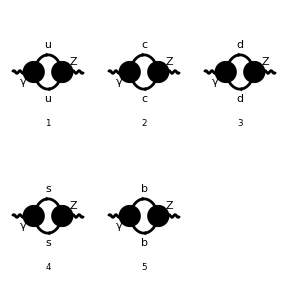

```mathematica
process3=V[1]-> V[2];
diagazlightquark=InsertFields[topoself,process3, InsertionLevel-> {Particles},ExcludeParticles->{F[1],V[1],V[2],V[3],V[4],S[1],S[2],S[3],U[1],U[2],U[3],U[4],SV[2],SV[3],F[2],F[3,{3}]},ExcludeFieldPoints-> FieldPoint[0][V[3],V[3],V[3],V[3]]];
Paint[diagazlightquark,SheetHeader->None,Numbering->Simple];
```

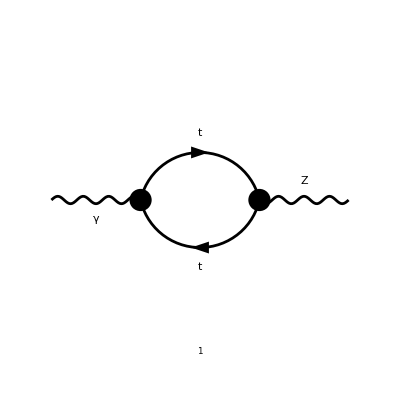

```mathematica
diagazheavyquark=InsertFields[topoself,process3,InsertionLevel->{Particles},ExcludeParticles->{F[1],V[1],V[2],V[3],V[4],S[1],S[2],S[3],U[1],U[2],U[3],U[4],SV[2],SV[3],F[2],F[3,{1}],F[3,{2}],F[4,{1}],F[4,{2}],F[4,{3}]},ExcludeFieldPoints-> FieldPoint[0][V[3],V[3],V[3],V[3]]];
Paint[diagazheavyquark,SheetHeader->None,Numbering->Simple];
```

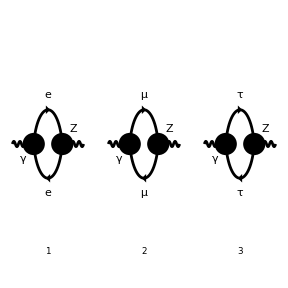

-(3 tr((-(γ·q)).((2 ⅈ √π √α γ^ν.(γ̄)^6 (sin(θ_W)))/(cos(θ_W))+(2 ⅈ √π √α γ^ν.(γ̄)^7 ((sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W)))).(γ·(k-q)).(2 ⅈ √π √α γ^μ.(γ̄)^6+2 ⅈ √π √α γ^μ.(γ̄)^7)))/(q^2.(q-k)^2)

```mathematica
diagazlepton=InsertFields[topoself,process3,InsertionLevel->{Particles},ExcludeParticles->{V[3],S[1],S[2],S[3],U[1],U[2],U[3],U[4],SV[2],SV[3],F[3],F[4]},ExcludeFieldPoints-> FieldPoint[0][V[3],V[3],V[3],V[3]]];
Paint[diagazlepton,SheetHeader->None,Numbering->Simple];
ampazfselflepton=FCFAConvert[CreateFeynAmp[diagazlepton, Truncated-> True, PreFactor ->-1], List-> False, SMP-> True, ChangeDimension->D,
IncomingMomenta->{k},OutgoingMomenta->{k}, LoopMomenta-> {q},DropSumOver-> True, LorentzIndexNames-> {μ,ν},
UndoChiralSplittings-> False, SMP-> True,FinalSubstitutions->{ SMP["m_mu"]-> 0,SMP["m_tau"]-> 0,SMP["m_u"]-> 0,SMP["m_d"]-> 0,SMP["m_e"]-> 0,SMP["m_c"]-> 0,SMP["m_s"]-> 0,SMP["m_b"]->0,SMP["e"]->Sqrt[4Pi SMP["alpha_fs"]]}]
```

```mathematica
ampazfselflightquark=FCFAConvert[CreateFeynAmp[diagazlightquark, Truncated-> True, PreFactor ->-1], List-> False, SMP-> True, ChangeDimension->D,
IncomingMomenta->{k},OutgoingMomenta->{k}, LoopMomenta-> {q},DropSumOver-> True, LorentzIndexNames-> {μ,ν},
UndoChiralSplittings-> False, SMP-> True,FinalSubstitutions->{ SMP["m_mu"]-> 0,SMP["m_u"]-> 0,SMP["m_d"]-> 0,SMP["m_e"]-> 0,SMP["m_c"]-> 0,SMP["m_s"]-> 0,SMP["m_b"]->0,SMP["e"]->Sqrt[4Pi SMP["alpha_fs"]]}]
```

-(2 tr((-(γ·q)).((2 ⅈ √π √α γ^ν.(γ̄)^7 (1/2-2/3 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))-(4 ⅈ √π √α γ^ν.(γ̄)^6 (sin(θ_W)))/(3 (cos(θ_W)))).(γ·(k-q)).(-4/3 ⅈ √π √α γ^μ.(γ̄)^6-4/3 ⅈ √π √α γ^μ.(γ̄)^7)))/(q^2.(q-k)^2)-(3 tr((-(γ·q)).((2 ⅈ √π √α γ^ν.(γ̄)^6 (sin(θ_W)))/(3 (cos(θ_W)))+(2 ⅈ √π √α γ^ν.(γ̄)^7 (1/3 (sin(θ_W))^2-1/2))/((cos(θ_W)) (sin(θ_W)))).(γ·(k-q)).(2/3 ⅈ √π √α γ^μ.(γ̄)^6+2/3 ⅈ √π √α γ^μ.(γ̄)^7)))/(q^2.(q-k)^2)

```mathematica
ampazfselfheavyquark=FCFAConvert[CreateFeynAmp[diagazheavyquark, Truncated-> True, PreFactor ->-1], List-> False, SMP-> True, ChangeDimension->D,
IncomingMomenta->{k},OutgoingMomenta->{k}, LoopMomenta-> {q},DropSumOver->True, LorentzIndexNames-> {μ,ν},
UndoChiralSplittings-> True, SMP-> True,FinalSubstitutions->{ SMP["m_mu"]-> 0,SMP["m_u"]-> 0,SMP["m_d"]-> 0,SMP["m_e"]-> 0,SMP["m_c"]-> 0,SMP["m_s"]-> 0,SMP["m_b"]->0,SMP["e"]->Sqrt[4Pi SMP["alpha_fs"]]}]
```

-(tr((m_t-γ·q).((2 ⅈ √π √α γ^ν.(γ̄)^7 (1/2-2/3 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))-(4 ⅈ √π √α γ^ν.(γ̄)^6 (sin(θ_W)))/(3 (cos(θ_W)))).(γ·(k-q)+m_t).(-4/3 ⅈ √π √α γ^μ)))/((q^2-m_t^2).((q-k)^2-m_t^2))

```mathematica
transverseleptonaz=1/(D-1)(Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]-Pair[LorentzIndex[μ,D],Momentum[k,D]]Pair[LorentzIndex[ν,D],Momentum[k,D]]/Pair[Momentum[k,D],Momentum[k,D]]). ampazfselflepton//Contract//DiracSimplify;

transverseleptonaz1=-ⅈ/(16 π^2) TID[transverseleptonaz/.DiracTrace-> Tr,q,ToPaVe-> True]//DiracSimplify
```

-(3 π α (2-D) k^2 (1-4 (sin(θ_W))^2) B_0(k^2,0,0))/(8 (1-D) (cos(θ_W)) (sin(θ_W)))

```mathematica
transverselightquarkaz=1/(D-1)(Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]-Pair[LorentzIndex[μ,D],Momentum[k,D]]Pair[LorentzIndex[ν,D],Momentum[k,D]]/Pair[Momentum[k,D],Momentum[k,D]]). ampazfselflightquark//Contract//DiracSimplify;
transverselightquarkaz1=-ⅈ/(16 π^2) TID[transverselightquarkaz/.DiracTrace-> Tr,q,ToPaVe-> True,Collecting-> True]//DiracSimplify
```

-(π α (2-D) k^2 (21-44 (sin(θ_W))^2) B_0(k^2,0,0))/(72 (1-D) (cos(θ_W)) (sin(θ_W)))

```mathematica
transverseheavyquarkaz=1/(D-1)(Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]-Pair[LorentzIndex[μ,D],Momentum[k,D]]Pair[LorentzIndex[ν,D],Momentum[k,D]]/Pair[Momentum[k,D],Momentum[k,D]]). ampazfselfheavyquark//Contract//DiracSimplify;
transverseheavyquarkaz1=-ⅈ/(16 π^2) TID[transverseheavyquarkaz/.DiracTrace-> Tr,q,ToPaVe-> True]
```

-(ⅈ ((8 ⅈ π^3 α (2-D) (3-8 (sin(θ_W))^2) A_0(m_t^2))/(9 (1-D) (cos(θ_W)) (sin(θ_W)))-(4 ⅈ π^3 α (3-8 (sin(θ_W))^2) (-D k^2+2 k^2-4 m_t^2) B_0(k^2,m_t^2,m_t^2))/(9 (1-D) (cos(θ_W)) (sin(θ_W)))))/(16 π^2)

```mathematica
ΣAZ[k_]=transverseheavyquarkaz1+transverselightquarkaz1+transverseleptonaz1/.Pair[Momentum[k,D],Momentum[k,D]]->k^2
```

-(ⅈ ((8 ⅈ π^3 α (2-D) (3-8 (sin(θ_W))^2) A_0(m_t^2))/(9 (1-D) (cos(θ_W)) (sin(θ_W)))-(4 ⅈ π^3 α (3-8 (sin(θ_W))^2) (-D k^2+2 k^2-4 m_t^2) B_0(k^2,m_t^2,m_t^2))/(9 (1-D) (cos(θ_W)) (sin(θ_W)))))/(16 π^2)-(π α (2-D) k^2 (21-44 (sin(θ_W))^2) B_0(k^2,0,0))/(72 (1-D) (cos(θ_W)) (sin(θ_W)))-(3 π α (2-D) k^2 (1-4 (sin(θ_W))^2) B_0(k^2,0,0))/(8 (1-D) (cos(θ_W)) (sin(θ_W)))

```mathematica
ΣAZ[0]//FullSimplify
```

-(π α (8 (sin(θ_W))^2-3) ((D-2) A_0(m_t^2)-2 m_t^2 B_0(0,m_t^2,m_t^2)))/(18 (D-1) (cos(θ_W)) (sin(θ_W)))

```mathematica
(*this is consistent with Radiative Corrections in Gauge Theories p70*)
```

```mathematica
uvsigaz=PaXEvaluateUV[ΣAZ[0],q]
```

0

```mathematica
PaXEvaluate[(D-2)A0[m^2]-2m^2B0[0,m^2,m^2]]
```

0

```mathematica
(*this is consistent with Radiative Corrections in Gauge Theories p70*)
```